```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
Quit[];
```

# PISANJE ENAČB

Ctrl+/     Ctrl+2     Ctrl+6     Ctrl+_     Shift+Enter     Alt+.     %     %%     %123

Esc+.......+Esc:  cross    tr    intt     dintt     sumt     prodt     a     b     g    j     p     ee     ii     dd     pd     prop     perp     ==>     -->     <==>     fa     ex    and     or     elem     reals     ints     rats     ...     un     inter

=.     Remove[]     Remove[“Global`*”]     Quit[]

Vgravene funkcije npr. Sin so z velko začetnico

MENI->Palettes->Basic Math Assistant

Vaja: pište random enačbe, dokler se ne  navadte. Na primer:

```mathematica
izraz1=(ArcSin@Log[5 α^(3/2),10]+(∫_-d^d dⅆd+∫_(🥐+🍩)^😁 (ⅇ^(ⅈ 🐷))ⅆ🐷)/(Cos[30°]+Cos@(π/6))+Limit[(1+1/n)^n,n->∞]/D[Sinh@x,x](Mod[5,3]Ceiling@√2)/(Floor[π]Round[√3]Binomial[3,2]))/((Γ D[(👽👻)_🍰+ⅇ^(🦄+Sin@🦄),🦄])/(Sign@Abs@Conjugate[μ/β+2 Λ/λ ⅈ]) Tanh@Log@√((1+1/φ+π/τ Δ)/(ρ+Ω)+√(trololo+((HOU🐶ϵΕ12🐶hou)/(mjav😺123🙀Mjav)+trololo/wupwup)/(trololo+trololo/trololo)))(∏_(j=1)^∞ 1/(1-1/(2j)^2))/(∑_(i=1)^∞ i^-4))
```

(ⅇ^(-🦄-Sin[🦄]) π^3 (1+√(trololo+((HOU🐶ϵΕ12🐶hou)/(mjav😺123🙀Mjav)+trololo/wupwup)/(1+trololo))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) Sign[Abs[(2 ⅈ Λ)/λ+μ/β]] (ArcSin[Log[10]/Log[5 α^(3/2)]]+2/9 ⅇ Sech[x]+(-ⅈ Cos[😁]+ⅈ Cos[🍩+🥐]+Sin[😁]-Sin[🍩+🥐])/(√3)))/(45 Γ (-1+√(trololo+((HOU🐶ϵΕ12🐶hou)/(mjav😺123🙀Mjav)+trololo/wupwup)/(1+trololo))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) (1+Cos[🦄]))

# IMENA SPREMENLJVIK

To je OK:

```mathematica
🐶AbC🦄🐧Čć🍟🍔šž🍟🍔Đδ🦆🎃γ🍓🫐🥝
```

🐶AbC🦄🐧Čć🍟🍔šž🍟🍔Đδ🦆🎃γ🍓🫐🥝

To NI OK. Sicer ne javi napake, ampak določene stvari ne delajo, če so indeksi v spremenljivkah:

```mathematica
Subscript[a, b]
```

a_b

To NI OK . Bomo pol vidli, kaj to v resnici pomeni

```mathematica
a_b
```

a_b

# POENOSTAVLJANJE

## Pogosto moramo podati predpostavk (assumptions)

```mathematica
FullSimplify[√(x^2)+√(y^2)]
FullSimplify[√(x^2)+√(y^2),{x>0,y>0}]
FullSimplify[√(x^2)+√(y^2),{x∈Reals,y∈Reals}]
FullSimplify[Sin[x],{x/π∈Integers}] (*VČASIH TUDI NE DELUJE!!!!!!!!!!!!!!*)
```

√(x^2)+√(y^2)

x+y

Abs[x]+Abs[y]

Sin[x]

## Simplify je hitrejši

```mathematica
AbsoluteTiming@Simplify@izraz1
```

{2.53741,(ⅇ^(-🦄-Sin[🦄]) π^3 (1+√(trololo+(mjav😺123🙀Mjav trololo+HOU🐶ϵΕ12🐶hou wupwup)/(mjav😺123🙀Mjav wupwup+mjav😺123🙀Mjav trololo wupwup))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) Sign[Abs[(2 ⅈ Λ)/λ+μ/β]] (ArcSin[Log[10]/Log[5 α^(3/2)]]+2/9 ⅇ Sech[x]+(-ⅈ Cos[😁]+ⅈ Cos[🍩+🥐]+Sin[😁]-Sin[🍩+🥐])/(√3)))/(45 Γ (-1+√(trololo+(mjav😺123🙀Mjav trololo+HOU🐶ϵΕ12🐶hou wupwup)/(mjav😺123🙀Mjav wupwup+mjav😺123🙀Mjav trololo wupwup))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) (1+Cos[🦄]))}

```mathematica
AbsoluteTiming@FullSimplify@izraz1
```

{19.6321,(ⅇ^(-🦄-Sin[🦄]) π^3 (1+√(trololo+(mjav😺123🙀Mjav trololo+HOU🐶ϵΕ12🐶hou wupwup)/(mjav😺123🙀Mjav wupwup+mjav😺123🙀Mjav trololo wupwup))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) (ArcSin[Log[10]/Log[5 α^(3/2)]]+2/9 ⅇ Sech[x]+(-ⅈ Cos[😁]+ⅈ Cos[🍩+🥐]+Sin[😁]-Sin[🍩+🥐])/(√3)))/(45 Γ (-1+√(trololo+(mjav😺123🙀Mjav trololo+HOU🐶ϵΕ12🐶hou wupwup)/(mjav😺123🙀Mjav wupwup+mjav😺123🙀Mjav trololo wupwup))+(1+(π Δ)/τ+1/φ)/(ρ+Ω)) (1+Cos[🦄]))}

## Ampak FullSimplify je boljši

prostornina tega poliedra, s stranico 1

```mathematica
formula = (5 (3+1/2 √(16-(1+√5+√(2 (5+√5) (4+1/2 (-5-√5)))-2 (-2+1/2 (5+√5)))^2)))/(√(3+1/4 (-16+(1+√5+√(2 (5+√5) (4+1/2 (-5-√5)))-2 (-2+1/2 (5+√5)))^2)))+5 (2+√((5+2 √5)/(2 (5+√5) (4+1/2 (-5-√5)))) (-2+1/2 (5+√5)) (-2+1/2 (5+√5)-√(3/2 (5+√5) (4+1/2 (-5-√5))))+1/2 √((5+2 √5) (16-(2+1/2 (-5-√5)+√(3/2 (5+√5) (4+1/2 (-5-√5))))^2))) √((5+2 √5)/(4-1/4 (√(2/((5+√5) (4+1/2 (-5-√5)))) (-2+1/2 (5+√5)) (-2+1/2 (5+√5)-√(3/2 (5+√5) (4+1/2 (-5-√5))))+√(16-(2+1/2 (-5-√5)+√(3/2 (5+√5) (4+1/2 (-5-√5))))^2))^2))+5 (2+1/2 (-1-√5-√(3/2 (5+√5) (4+1/2 (-5-√5)))+3 (-2+1/2 (5+√5)))+1/2 √(3 (16-(1+√5+√(3/2 (5+√5) (4+1/2 (-5-√5)))-3 (-2+1/2 (5+√5)))^2))) √(3/(4-1/4 ((-1-√5-√(3/2 (5+√5) (4+1/2 (-5-√5)))+3 (-2+1/2 (5+√5)))/(√3)+√(16-(1+√5+√(3/2 (5+√5) (4+1/2 (-5-√5)))-3 (-2+1/2 (5+√5)))^2))^2));

Poenostavitev1 = Simplify@formula
Poenostavitev2 = FullSimplify@formula
```

(5 (6+√(2 (3+√5))))/(√(6-2 √5))+5/4 (9+√5-√(30-6 √5)+√(6 (14+2 √5+√(30-6 √5)+√(30 (5-√5))))) √(3/(4-1/4 ((1+√5-√(30-6 √5))/(2 √3)+1/(√(2/(√(30-6 √5)+√(30 (5-√5))+2 (7+√5)))))^2))+5/4 (16+3 √(14+6 √5)-2 √(15+6 √5)+√(70+30 √5)-2 √(75+30 √5)+2 √(2 (90+38 √5+15 √(30-6 √5)+7 √(30 (5-√5))))) √((5+2 √5)/(16-(((1+√5) (1+√5-√(30-6 √5)))/(2 √(10-2 √5))+1/(√(2/(√(30-6 √5)+√(30 (5-√5))+2 (7+√5)))))^2))

95+50 √5

## Rezultata sta enaka, sta pa zapisana drugače

```mathematica
FullSimplify[Poenostavitev1==Poenostavitev2]
Poenostavitev1===Poenostavitev2

(*s klicajem ! pa zanikamo*)

FullSimplify[Poenostavitev1!=Poenostavitev2]
Poenostavitev1=!=Poenostavitev2
```

True

False

False

True

## Morda pa nas zanima samo Numerična (decimalna) vrednost.

```mathematica
N@formula
1.0 formula
1. formula
0.9999999999999999 formula
.99999999999999999 formula
(1+0.ⅈ)formula
```

206.803

206.803

206.803

«2 more identical outputs»

206.803+0. ⅈ

## ČE VAS ZANIMA SAMO DECIMALNI ŠTEVILSKI REZULT, NPR. PRI FIZIKI, POTEM RAČUNAJTE VSE S ŠTEVILI V TAKI OBLIKI, KER JE TO VEČ REDOV HITREJE.

# ZA VMES (VEČ O TEMU KASNEJE)

Seznami

```mathematica
s={1,2,3,{4,5}};
s[[2]] 
s[[-1]]
s[[4,1]]
```

2

{4,5}

4

Zamenjave

```mathematica
√((x+y)/(z-Log@x+Sin[x]^2))/.{x->2,y->3}
x
y
```

√5 √(1/(z-Log[2]+Sin[2]^2))

x

y

# REŠEVANJE ENAČB

## Solve: Osnoven, analitično

```mathematica
FullSimplify@Solve[
{x^2+y^2==R^2,   y==a x+b},
{x,y}
]
```

{{x→-(a b+√(-b^2+(1+a^2) R^2))/(1+a^2),y→(b-a √(-b^2+(1+a^2) R^2))/(1+a^2)},{x→(-a b+√(-b^2+(1+a^2) R^2))/(1+a^2),y→(b+a √(-b^2+(1+a^2) R^2))/(1+a^2)}}

```mathematica
{x,y}/.%
```

{{-(a b+√(-b^2+(1+a^2) R^2))/(1+a^2),(b-a √(-b^2+(1+a^2) R^2))/(1+a^2)},{(-a b+√(-b^2+(1+a^2) R^2))/(1+a^2),(b+a √(-b^2+(1+a^2) R^2))/(1+a^2)}}

```mathematica
%[[2,1]]    (* 2. rešitev, 1. neznanka*)
```

(-a b+√(-b^2+(1+a^2) R^2))/(1+a^2)

```mathematica
Solve[{x^2+2 y^3==3681,  x>0,  y>0},{x,y},Integers]
```

{{x→15,y→12},{x→41,y→10},{x→57,y→6}}

```mathematica
Solve[x^2 + y^2 < +30, {x, y},Integers]
```

{{x→-5,y→-2},{x→-5,y→-1},{x→-5,y→0},{x→-5,y→1},{x→-5,y→2},{x→-4,y→-3},{x→-4,y→-2},{x→-4,y→-1},{x→-4,y→0},{x→-4,y→1},{x→-4,y→2},{x→-4,y→3},{x→-3,y→-4},{x→-3,y→-3},{x→-3,y→-2},{x→-3,y→-1},{x→-3,y→0},{x→-3,y→1},{x→-3,y→2},{x→-3,y→3},{x→-3,y→4},{x→-2,y→-5},{x→-2,y→-4},{x→-2,y→-3},{x→-2,y→-2},{x→-2,y→-1},{x→-2,y→0},{x→-2,y→1},{x→-2,y→2},{x→-2,y→3},{x→-2,y→4},{x→-2,y→5},{x→-1,y→-5},{x→-1,y→-4},{x→-1,y→-3},{x→-1,y→-2},{x→-1,y→-1},{x→-1,y→0},{x→-1,y→1},{x→-1,y→2},{x→-1,y→3},{x→-1,y→4},{x→-1,y→5},{x→0,y→-5},{x→0,y→-4},{x→0,y→-3},{x→0,y→-2},{x→0,y→-1},{x→0,y→0},{x→0,y→1},{x→0,y→2},{x→0,y→3},{x→0,y→4},{x→0,y→5},{x→1,y→-5},{x→1,y→-4},{x→1,y→-3},{x→1,y→-2},{x→1,y→-1},{x→1,y→0},{x→1,y→1},{x→1,y→2},{x→1,y→3},{x→1,y→4},{x→1,y→5},{x→2,y→-5},{x→2,y→-4},{x→2,y→-3},{x→2,y→-2},{x→2,y→-1},{x→2,y→0},{x→2,y→1},{x→2,y→2},{x→2,y→3},{x→2,y→4},{x→2,y→5},{x→3,y→-4},{x→3,y→-3},{x→3,y→-2},{x→3,y→-1},{x→3,y→0},{x→3,y→1},{x→3,y→2},{x→3,y→3},{x→3,y→4},{x→4,y→-3},{x→4,y→-2},{x→4,y→-1},{x→4,y→0},{x→4,y→1},{x→4,y→2},{x→4,y→3},{x→5,y→-2},{x→5,y→-1},{x→5,y→0},{x→5,y→1},{x→5,y→2}}

```mathematica
Solve[Sin@x==0,x]
```

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[x^2 + y^2 < 1, {x, y}]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

## Reduce: naprednejši, analitično

Razume tudi take neenakosti

```mathematica
Reduce[x^2 + y^2 < 1, {x, y}]
```

-1<x<1&&-√(1-x^2)<y<√(1-x^2)

```mathematica
(*Če mamo diskretne rešitve, jih tako pretvorimo v enako obliko, kot pri Solve*)
{ToRules@Reduce[x^2 + y^2 < 30, {x, y},Integers]}
```

{{x→-5,y→-2},{x→-5,y→-1},{x→-5,y→0},{x→-5,y→1},{x→-5,y→2},{x→-4,y→-3},{x→-4,y→-2},{x→-4,y→-1},{x→-4,y→0},{x→-4,y→1},{x→-4,y→2},{x→-4,y→3},{x→-3,y→-4},{x→-3,y→-3},{x→-3,y→-2},{x→-3,y→-1},{x→-3,y→0},{x→-3,y→1},{x→-3,y→2},{x→-3,y→3},{x→-3,y→4},{x→-2,y→-5},{x→-2,y→-4},{x→-2,y→-3},{x→-2,y→-2},{x→-2,y→-1},{x→-2,y→0},{x→-2,y→1},{x→-2,y→2},{x→-2,y→3},{x→-2,y→4},{x→-2,y→5},{x→-1,y→-5},{x→-1,y→-4},{x→-1,y→-3},{x→-1,y→-2},{x→-1,y→-1},{x→-1,y→0},{x→-1,y→1},{x→-1,y→2},{x→-1,y→3},{x→-1,y→4},{x→-1,y→5},{x→0,y→-5},{x→0,y→-4},{x→0,y→-3},{x→0,y→-2},{x→0,y→-1},{x→0,y→0},{x→0,y→1},{x→0,y→2},{x→0,y→3},{x→0,y→4},{x→0,y→5},{x→1,y→-5},{x→1,y→-4},{x→1,y→-3},{x→1,y→-2},{x→1,y→-1},{x→1,y→0},{x→1,y→1},{x→1,y→2},{x→1,y→3},{x→1,y→4},{x→1,y→5},{x→2,y→-5},{x→2,y→-4},{x→2,y→-3},{x→2,y→-2},{x→2,y→-1},{x→2,y→0},{x→2,y→1},{x→2,y→2},{x→2,y→3},{x→2,y→4},{x→2,y→5},{x→3,y→-4},{x→3,y→-3},{x→3,y→-2},{x→3,y→-1},{x→3,y→0},{x→3,y→1},{x→3,y→2},{x→3,y→3},{x→3,y→4},{x→4,y→-3},{x→4,y→-2},{x→4,y→-1},{x→4,y→0},{x→4,y→1},{x→4,y→2},{x→4,y→3},{x→5,y→-2},{x→5,y→-1},{x→5,y→0},{x→5,y→1},{x→5,y→2}}

```mathematica
{ToRules@Reduce[a x^2+b x+c==0,x]}
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)},{a→0,x→-c/b},{c→0,b→0,a→0}}

SKRATKA SO RAZLIKE, AMPAK VEČINOMA SE OBNAŠA, KOT MALO NAPREDNEJŠI SOLVE. 
Za več podrobnosti glej https://mathematica.stackexchange.com/questions/17127/what-is-the-difference-between-reduce-and-solve

## NSolve: Numerično, poskuša najti več rešitev

Uporablja se enako, kot Solve

Numerične rešitve

## FindRoot: Numerično, ena rešitev, kot Newtonov algoritem

Tisto eno rešitev najde zelo hitro, uporabljamo ga vglavnem, ko hočmo zelo hitro reševat enačbe in približno vemo, kje začet iskat. Tipičen primer, ko iščemo trke kdaj in kje trčijo predmeti.

Deluje za zelo splošne stvari

Ampak treba vedet dost natančno, kje štartat

Na primer tuki štartamo na -1-ⅈ.

Če za štart napišemo realno, išče v realnem

```mathematica
FindRoot[{3 x^2+2x+1},{{x,-1-ⅈ}}]
```

{x→-0.333333-0.471405 ⅈ}

Če ne vemo dos natančno, kje začet iskat lahko na ta način sprobamo več točk:

To boste razumeli kasneje

```mathematica
St=3;
enačbe={poli1,poli2}=Table[Total@Total@Table[RandomReal[] x^i1  y^i2,{i1,0,St},{i2,0,St}],2];
ran={{-2,2,.1},{-2,2,.1}};
ϵ=.00001;



sol1=Quiet@Flatten[Table[   (*vse rešitve, tudi narobne, oblika rulsov*)
	FindRoot[enačbe,{{x,x0},{y,y0}}],
{x0,ran[[1,1]],ran[[1,2]],ran[[1,3]]},
{y0,ran[[2,1]],ran[[2,2]],ran[[2,3]]}
],1];
sol2={x,y}/.Select[sol1,Norm[enačbe/.#]<ϵ&];   (*pravilne točke, ampak se podvajajo*)
sol3=Mean/@Gather[sol2,Norm[#1-#2]<2ϵ&];     (*pravilne točke*)





sol33D={Splice@#,0}&/@sol3;
plot1=Plot3D[
	{poli1,poli2,0},{x,ran[[1,1]],ran[[1,2]]},{y,ran[[2,1]],ran[[2,2]]},
	PlotPoints->100,Mesh->None,PlotStyle->Directive[Opacity@.8]
];
Show[
	plot1,
	Graphics3D[{Red, Sphere[sol33D,.1]}]
]
```

-Graphics3D-

Ampak seveda, če ne vemo dobr, kje začet iskat in če NSolve deluje, pol uporabmo NSolve.

```mathematica
sol3=Select[{x,y}/.NSolve[poli1==poli2==0,{x,y}],Norm@Im@#<ϵ&];

sol33D={Splice@#,0}&/@sol3;
plot1=Plot3D[
	{poli1,poli2,0},{x,ran[[1,1]],ran[[1,2]]},{y,ran[[2,1]],ran[[2,2]]},
	PlotPoints->100,Mesh->None,PlotStyle->Directive[Opacity@.8]
];
Show[
	plot1,
	Graphics3D[{Red, Sphere[sol33D,.1]}]
]
```

-Graphics3D-

# ∫NTEGR∫RANJE

## ANALITIČNO

To dela brez problema

```mathematica
∫(r (r^2+h^2)^(-3/2))ⅆr
```

-1/(√(h^2+r^2))

To melje in melje, preden dobimo rezultat, to je, ker računa čisto splošno v kompleksnem

```mathematica
∫_R1^R2 (r (r^2+h^2)^(-3/2))ⅆr
```

ConditionalExpression[1/(√(h^2+R1^2))-1/(√(h^2+R2^2)), ]

Lahko napišemo predpostavke:

```mathematica
Integrate[(r (r^2+h^2)^(-3/2)),{r,R1,R2},Assumptions->{0<R1<R2, h<0}]
```

1/(√(h^2+R1^2))-1/(√(h^2+R2^2))

Če to kdaj ne dela,  pa samo izračunamo nedoločni ∫  in vstavimo meje

```mathematica
ned=∫(r (r^2+h^2)^(-3/2))ⅆr;
(ned/.r->R2)-(ned/.r->R1)
```

1/(√(h^2+R1^2))-1/(√(h^2+R2^2))

## NUMERIČNO

```mathematica
{R1,R2}={1,2};
h=3;
NIntegrate[(r (r^2+h^2)^(-3/2)),{r,R1,R2}]
```

0.0388777

Želena natančnost rezultata in delavna natančnost

```mathematica
NIntegrate[
	(r (r^2+h^2)^(-3/2)),  {r,R1,R2},
	PrecisionGoal->20, WorkingPrecision->30
]
```

0.0388776679042233721907184877148

Lahko tudi po več spremenljivkah, isto pri

```mathematica
h=.;   (*tako počistimo h*)
{H1,H2}={3,4};

NIntegrate[
	(r (r^2+h^2)^(-3/2)),  {r,R1,R2},  {h,H1,H2},
	PrecisionGoal->10, WorkingPrecision->30
]
```

0.0273938301373054157230660974678

# DIFERENCIALNE ENAČBE

## ANALITIČNO

npr. nihajna enačba

```mathematica
Remove["Global`*"];

sol=s[t]/.DSolve[{
  s''[t]==-ω^2 s[t],   s'[0]==v0,   s[0]==s0
}, s[t], t][[1]]
```

(s0 ω Cos[t ω]+v0 Sin[t ω])/ω

## NUMERIČNO

npr. gibanje predmeta na elastiki, linearni upor

```mathematica
Remove["Global`*"];
g[t_?NumericQ]:={0,0,-9.81};
c1=.1;
ω=3.2;
l0=1;

r0={3,2,0};
v0=3{-2,3,0};
t1=100;   (*računamo za 10s*)


sol=NDSolve[
	{r''[t]  ==  g[t] - ω^2 (Norm@r[t]-l0) Normalize@r[t] - c1 r'[t],   r'[0]==v0,   r[0]==r0}, 
r[t], {t,0,t1}][[1]];

rr[tt_]:= (Evaluate[r[t]/.sol])/.t->tt;

rr@1.2345678
```

{-2.12657,-2.64735,-2.41516}

```mathematica
Show[
	ParametricPlot3D[rr[t],{t,0,t1},PlotRange->All,PlotPoints->100],
	Graphics3D@Point@{r0,{0,0,0}},
	Graphics3D@Line@{r0,{0,0,0}}
]
```

-Graphics3D-

## PDE-JI IN OSTALE NAPREDNEJŠE STVARI:

to zahteva še druga znanja, se še vrnemo na to

sicer pa dokumentacija: https://reference.wolfram.com/language/ref/NDSolve.html

# POLINOMI

```mathematica
p1=Times@@(x+RandomInteger[{-5,5},20])
p2=Times@@(x+RandomInteger[{-5,5},10])
```

(-5+x) (-4+x) (-3+x) (-2+x)^3 (-1+x) x^2 (2+x)^4 (3+x) (4+x) (5+x)^5

(-5+x) (-4+x) (-1+x) x (1+x) (2+x) (3+x)^2 (4+x) (5+x)

poračunamo

```mathematica
Expand@p1
```

-288000000 x^2-86400000 x^3+467600000 x^4+223800000 x^5-248596000 x^6-161833360 x^7+50779112 x^8+51892484 x^9-612750 x^10-8109943 x^11-1239219 x^12+566488 x^13+170364 x^14-8438 x^15-8174 x^16-692 x^17+106 x^18+21 x^19+x^20

razstavimo

```mathematica
Factor@%
```

(-5+x) (-4+x) (-3+x) (-2+x)^3 (-1+x) x^2 (2+x)^4 (3+x) (4+x) (5+x)^5

delimo:

```mathematica
PolynomialQuotientRemainder[p1,p2,x]
```

{19824+24176 x-20176 x^2-12224 x^3+7104 x^4+2540 x^5-836 x^6-285 x^7+23 x^8+13 x^9+x^10,142732800 x+52588800 x^2-122514912 x^3-80097552 x^4-1314576 x^5+7788960 x^6+1035072 x^7-186768 x^8-31824 x^9}

```mathematica
Print/@%;
```

19824+24176 x-20176 x^2-12224 x^3+7104 x^4+2540 x^5-836 x^6-285 x^7+23 x^8+13 x^9+x^10

142732800 x+52588800 x^2-122514912 x^3-80097552 x^4-1314576 x^5+7788960 x^6+1035072 x^7-186768 x^8-31824 x^9

nekaj podobnega razstavljanju:

```mathematica
st=3;
p3=Total@Total@Table[RandomInteger[{-5,5}] x^i1  y^i2,{i1,0,St},{i2,0,St}]
```

5-5 x-2 x^2-x^3-2 y-2 x y-2 x^2 y+2 x^3 y+5 y^2+x^2 y^2+4 x^3 y^2+4 y^3-5 x y^3+4 x^2 y^3+x^3 y^3

```mathematica
Collect[p3,x]
```

5-2 y+5 y^2+4 y^3+x (-5-2 y-5 y^3)+x^3 (-1+2 y+4 y^2+y^3)+x^2 (-2-2 y+y^2+4 y^3)

koeficienti

```mathematica
CoefficientList[p3, {x,y}]
```

{{5,-2,5,4},{-5,-2,0,-5},{-2,-2,1,4},{-1,2,4,1}}

```mathematica
MatrixForm@%
```

(5 | -2 | 5 | 4
-5 | -2 | 0 | -5
-2 | -2 | 1 | 4
-1 | 2 | 4 | 1)

# VRSTE

## ENA SPREMENLJIVKA

```mathematica
Remove@f;
f[x_] := Sin[x];
stopnja=8;

Series[f[x],{x,x0,stopnja}]
```

Sin[x0]+Cos[x0] (x-x0)-1/2 Sin[x0] (x-x0)^2-1/6 Cos[x0] (x-x0)^3+1/24 Sin[x0] (x-x0)^4+1/120 Cos[x0] (x-x0)^5-1/720 Sin[x0] (x-x0)^6-(Cos[x0] (x-x0)^7)/5040+(Sin[x0] (x-x0)^8)/40320+O[x-x0]^9

```mathematica
p=Normal@%
Short@p
```

(x-x0) Cos[x0]-1/6 (x-x0)^3 Cos[x0]+1/120 (x-x0)^5 Cos[x0]-((x-x0)^7 Cos[x0])/5040+Sin[x0]-1/2 (x-x0)^2 Sin[x0]+1/24 (x-x0)^4 Sin[x0]-1/720 (x-x0)^6 Sin[x0]+((x-x0)^8 Sin[x0])/40320

(x-x0) Cos[x0]-1/6 (x-x0)^3 Cos[x0]+«9»+((x-x0)^8 Sin[x0])/40320

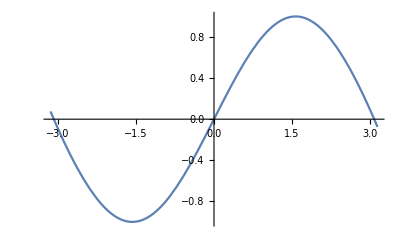

```mathematica
Plot[p/.x0->0,{x,-π,π}]
```

## VEČ SPREMENLJIVK

```mathematica
Remove@f;
f[x_, y_] := Sin[x]Cos[y];
X={x,y};
X0={x0,y0};
stopnja=15;

(*spomnimo se začetka izpeljave iz matematike 1:*)
p=Normal@Series[(f@@X)/. Thread[X->X0+t (X-X0)],{t,0,stopnja}]/. t->1;
Short@p
```

(x-x0) Cos[x0] Cos[y0]-1/6 (x-x0)^3 Cos[x0] Cos[y0]+«201»+((«1»)^12 «3»)/479001600-((x-x0)^14 (-y+y0) Sin[x0] Sin[y0])/87178291200

```mathematica
Plot3D[
	(p/.Thread[X0->{0,0}]),{x,-π,π},{y,-π,π},
	PlotPoints->100, PlotStyle->Directive[Cyan]
]
```

-Graphics3D-

# FITANJE

```mathematica
meritve = {{0, 1}, {1, 0}, {3, 2}, {5, 4}, {6, 4}, {7, 5}};

nlm = NonlinearModelFit[meritve, Log[a + b x^2], {{a,2}, {b,1.5}}, x]
nlm["ParameterTable"]
nlm["ParameterTableEntries"]
Normal@nlm
```

FittedModel[Log[1.50632+1.42633 x^2]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.50632 | 1.10159 | 1.36741 | 0.243294
b | 1.42633 | 0.600123 | 2.37673 | 0.0762602

{{1.50632,1.10159,1.36741,0.243294},{1.42633,0.600123,2.37673,0.0762602}}

Log[1.50632+1.42633 x^2]

```mathematica
nlm=NonlinearModelFit[data,enačba,parametri,sprem];
(*
nlm["ParameterTable"];           (*tabela podatkov fita*)
nlm["ParameterTableEntries"];    (*vrednosti iz tabele -||-*)
Normal@nlm                       (*enačba*)
*)
```

```mathematica
data = {{0.1, 0.9, 0.2}, {0, 0.3, 0.5}, {0.8, 0.6, 2.7}, {0.7, 0.8, 1.8}};
nlm = NonlinearModelFit[data, Exp[a x - b y], {a, b}, {x, y}]
```

FittedModel[ⅇ^(2.35955 x-1.44296 y)]

# INTERPOLACIJA IN ISKANJE VRHOV

```mathematica
xji=Subdivide[-10,10,41];
točke=N@{xji,Cos[xji]}ᵀ
```

{{-10.,-0.839072},{-9.5122,-0.996182},{-9.02439,-0.92091},{-8.53659,-0.630815},{-8.04878,-0.193569},{-7.56098,0.288831},{-7.07317,0.703856},{-6.58537,0.95469},{-6.09756,0.982821},{-5.60976,0.781688},{-5.12195,0.398208},{-4.63415,-0.0781628},{-4.14634,-0.5363},{-3.65854,-0.869334},{-3.17073,-0.999575},{-2.68293,-0.896644},{-2.19512,-0.58455},{-1.70732,-0.136097},{-1.21951,0.344104},{-0.731707,0.744035},{-0.243902,0.970403},{0.243902,0.970403},{0.731707,0.744035},{1.21951,0.344104},{1.70732,-0.136097},{2.19512,-0.58455},{2.68293,-0.896644},{3.17073,-0.999575},{3.65854,-0.869334},{4.14634,-0.5363},{4.63415,-0.0781628},{5.12195,0.398208},{5.60976,0.781688},{6.09756,0.982821},{6.58537,0.95469},{7.07317,0.703856},{7.56098,0.288831},{8.04878,-0.193569},{8.53659,-0.630815},{9.02439,-0.92091},{9.5122,-0.996182},{10.,-0.839072}}

## Interpolation: ustveri funkcijo: polinomska interpolacija čez točke

Ta dobljena funkcija se v kakih ukazih čudno obnaša in je treba še  kej dodatno čarat

Učasih se interpolacijo enostavno bolj splača tabelirati in delati z diskeretnimi metodami. To se bomo naučili pri seznamih.

```mathematica
f=Interpolation[točke, InterpolationOrder->4];
f@.56789
fodv[y_]:=D[f[x],x]/.x->y;
fodv[3]
```

0.84287

-0.141076

## FindMaximum dela podobno, kot FindRoot

```mathematica
maks=FindMaximum[f[x],{x,.5}]   (*Najde enega, kot find root*)
```

{0.999937,{x→-1.29893×10^-8}}

Tudi za f več spremenljivk, na poljubnih regionsih

## FindPeaks: Najde vrhove, ampak prva koordinata je indeks

FindPeaks[seznam1D, red glajenja, ostrina, vrednostna meja, InterpolationOrder->]

https://reference.wolfram.com/language/ref/FindPeaks.html

```mathematica
fp=FindPeaks[točke[[;;,2]],3,InterpolationOrder->2]
```

{{8.6227,0.99963},{21.5,0.999549},{34.3773,0.99963}}

Če hočemo dejanske koordinate in ne indeksa:

```mathematica
kord[ind_]=točke[[1,1]]+(ind-1)/(Length@točke-1)(točke[[-1,1]]-točke[[1,1]]);
vrhovi={kord@fp[[;;,1]],fp[[;;,2]]}ᵀ
```

{{-6.28161,0.99963},{0.,0.999549},{6.28161,0.99963}}

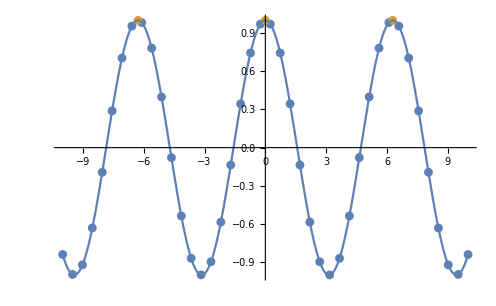

```mathematica
Show[
	ListPlot@{točke,vrhovi},
	Plot[f[x],{x,-10,10}]
]
```

```mathematica
Remove@f;
f=Sin[#1]Cos[#2]&;
{xmin,xmax,ymin,ymax}=5{-1,1,-1,1};
{dx,dy}=.5{1,1};

Xji=Flatten[Table[{x,y},{x,xmin,xmax,dx},{y,ymin,ymax,dy}],1];
fji=f@@@Xji;
ttočke={Xji,fji}ᵀ;
Short@ttočke
```

{{{-5.,-5.},0.272011},{{-5.,-4.5},-0.202137},«438»,{{5.,5.},-0.272011}}

```mathematica
fint=Interpolation[ttočke,InterpolationOrder->3];

fint[3,4]

Plot3D[
	fint[x,y],{x,xmin,xmax},{y,ymin,ymax},
	PlotPoints->100, PlotStyle->Directive[Cyan]
]
```

-0.0922422

-Graphics3D-

# PRIKAZANA MESTA

```mathematica
stopi=100.0 π;
nst=5;

NumberForm[stopi,nst]
NumberForm[stopi,{3,nst}]
NumberForm[stopi,{100,nst}]

ScientificForm[stopi,nst]
```

314.16

314.00000

314.15927

3.1416×10^2

# NAPAKE, ENOTE, ČAS

te stvari se uporablja bol redko, ampak včasih pa pride prav

```mathematica
a1=Around[x1,dx1]
a2=Around[x2,dx2]
a1+a2
```

x1dx1

x2dx2

x1+x2√(dx1^2+dx2^2)

```mathematica
Quantity[6,"Meters"]/Quantity[2,"Seconds"]
```

3 m/s

```mathematica
QuantityMagnitude@%
```

3

```mathematica
QuantityUnit@%%
```

Meters/Seconds

```mathematica
Now
```

Mon 22 Aug 2022 22:33:07GMT+2

za astronomske naloge tipa kdaj bo...?

```mathematica
Now + Quantity[1.23 10^8,"Seconds"]
```

Thu 16 Jul 2026 13:15:56GMT+2

```mathematica
{leto,mesec,dan,h,min,s}={2077,1,23,4,56,7};

čas=DateObject[{leto,mesec,dan,h,min,s}]
DateString@čas
```

Sat 23 Jan 2077 04:56:07GMT+2

Sat 23 Jan 2077 04:56:07

# DRUGO

nastopajoče spremenljivke

to uporabljajte kot črno škatlo

```mathematica
Spremenljivke[izraz_]:=With[
	{globalQ=Context@#==="Global`"&},
	DeleteDuplicates@Cases[izraz,_Symbol?globalQ,Infinity]
];

Spremenljivke[(🐷123+∫_(🥐+🍩)^😁 (ⅇ^(ⅈ 🐷))ⅆ🐷)/(Cos[30°]+Cos@(π/6))+Limit[(1+1/n)^n,n->∞]/D[Sinh@x,x](Γ D[(👽👻)_🍰+ⅇ^(🦄+Sin@🦄),🦄])/(Sign@Abs@Conjugate[μ/β+2 Λ/λ ⅈ])]
```

{🦄,Γ,x,λ,Λ,β,μ,🐷123,😁,🍩,🥐}

polarne koordinate

```mathematica
FromPolarCoordinates@{1,π/3}
FromPolarCoordinates@{1,60°}
FromPolarCoordinates@{R,α,β}

ToPolarCoordinates@{1,2,3}
ToPolarCoordinates@{-1,-2,-3}
```

{1/2,(√3)/2}

{1/2,(√3)/2}

{R Cos[α],R Cos[β] Sin[α],R Sin[α] Sin[β]}

{√14,ArcCos[1/(√14)],ArcTan[3/2]}

{√14,ArcCos[-1/(√14)],-π+ArcTan[3/2]}

divergenca, rotor

```mathematica
polje={Sin[a x1 x2], Log@x3, Tanh[b x2] x3^-3 x1};
Div[polje,{x1,x2,x3}]
Curl[polje,{x1,x2,x3}]
```

a x2 Cos[a x1 x2]-(3 x1 Tanh[b x2])/x3^4

{-1/x3+(b x1 Sech[b x2]^2)/x3^3,-Tanh[b x2]/x3^3,-a x1 Cos[a x1 x2]}